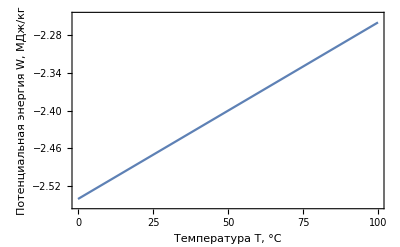

```mathematica
linear=Plot[-L-c(T0-T)+(3R(T0-T))/μ/.L->2.260/.c->avcap 10^-3/.T0->100/.R->8.314/.μ->18 10^3,{T,0,100},ImageSize->{1000},PlotRange->{{0,100},{-2.55,-2.25}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Температура T, °C",28,FontFamily->"Times New Roman"],Style["Потенциальная энергия W, МДж/кг",28,FontFamily->"Times New Roman"]}]
```

```mathematica
pts={{0.01,4.21},{5,4.204},{10,4.193},{15,4.1855},{20,4.183},{25,4.181},{30,4.179},{35,4.178},{40,4.179},{45,4.181},{50,4.182},{55,4.183},{60,4.185},{65,4.188},{70,4.191},{75,4.194},{80,4.198},{85,4.203},{90,4.208},{95,4.213},{100,4.219}}
```

{{0.01,4.21},{5,4.204},{10,4.193},{15,4.1855},{20,4.183},{25,4.181},{30,4.179},{35,4.178},{40,4.179},{45,4.181},{50,4.182},{55,4.183},{60,4.185},{65,4.188},{70,4.191},{75,4.194},{80,4.198},{85,4.203},{90,4.208},{95,4.213},{100,4.219}}

```mathematica
cap=Interpolation[pts]
```

InterpolatingFunction[{{0.01, 100.}}, <>]

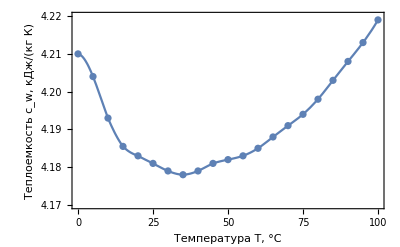

```mathematica
capacity=Show[Plot[cap[t],{t,0.01,100},PlotRange->{{0,100},{4.17,4.22}},ImageSize->{500},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[16,FontFamily->"Times New Roman"],FrameLabel->{Style["Температура T, °C",20,FontFamily->"Times New Roman"],Style["Теплоемкость c_w, кДж/(кг К)",20,FontFamily->"Times New Roman"]}],ListPlot[pts,PlotStyle->Directive[PointSize[0.013]]]]
```

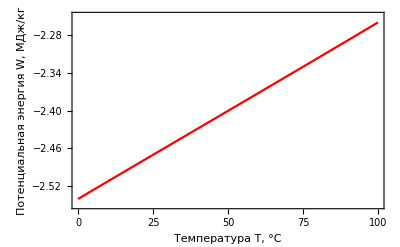

```mathematica
interp=Plot[-L-0.001Integrate[cap[t],{t,T,100}]+(3R(T0-T))/μ/.L->2.260/.c->4.19 10^-3/.T0->100/.R->8.314/.μ->18 10^3,{T,0.01,100},ImageSize->{1000},PlotRange->{{0,100},{-2.55,-2.25}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Температура T, °C",28,FontFamily->"Times New Roman"],Style["Потенциальная энергия W, МДж/кг",28,FontFamily->"Times New Roman"]},PlotStyle->Red]
```

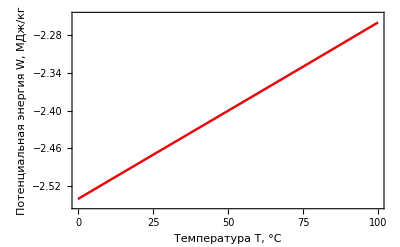

```mathematica
Show[linear,interp]
```

```mathematica
avcap=1/99.99 Integrate[cap[t],{t,0.01,100}]
```

4.19112

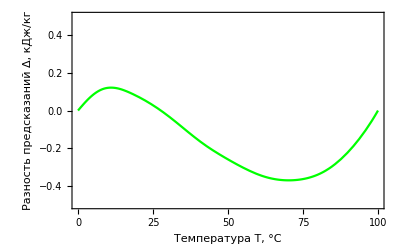

```mathematica
dif=Plot[avcap(100-T)-Integrate[cap[t],{t,T,100}],{T,0.01,100},ImageSize->{1000},PlotRange->{{0,100},{-0.5,0.5}},Axes->{True,False},Frame->True,AxesLabel->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Температура T, °C",28,FontFamily->"Times New Roman"],Style["Разность предсказаний Δ, кДж/кг",28,FontFamily->"Times New Roman"]},PlotStyle->Green]
```

```mathematica
lineareng=Plot[-L-c(T0-T)+(3R(T0-T))/μ/.L->2.260/.c->avcap 10^-3/.T0->100/.R->8.314/.μ->18 10^3,{T,0,100},ImageSize->{1000},PlotRange->{{0,100},{-2.55,-2.25}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Temperature T, °C",28,FontFamily->"Times New Roman"],Style["Potential energy W, MJ/kg",28,FontFamily->"Times New Roman"]}]
```

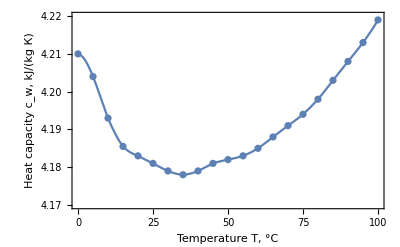

```mathematica
capacityeng=Show[Plot[cap[t],{t,0.01,100},PlotRange->{{0,100},{4.17,4.22}},ImageSize->{500},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[16,FontFamily->"Times New Roman"],FrameLabel->{Style["Temperature T, °C",20,FontFamily->"Times New Roman"],Style["Heat capacity c_w, kJ/(kg К)",20,FontFamily->"Times New Roman"]}],ListPlot[pts,PlotStyle->Directive[PointSize[0.013]]]]
```

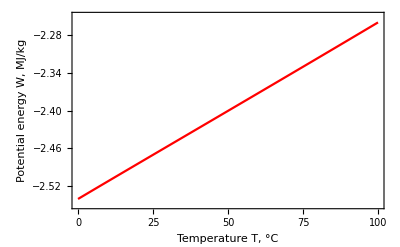

```mathematica
interpeng=Plot[-L-0.001Integrate[cap[t],{t,T,100}]+(3R(T0-T))/μ/.L->2.260/.c->4.19 10^-3/.T0->100/.R->8.314/.μ->18 10^3,{T,0.01,100},ImageSize->{1000},PlotRange->{{0,100},{-2.55,-2.25}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Temperature T, °C",28,FontFamily->"Times New Roman"],Style["Potential energy W, MJ/kg",28,FontFamily->"Times New Roman"]},PlotStyle->Red]
```

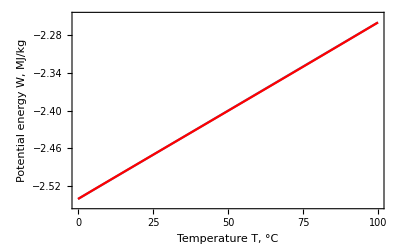

```mathematica
Show[lineareng,interpeng]
```

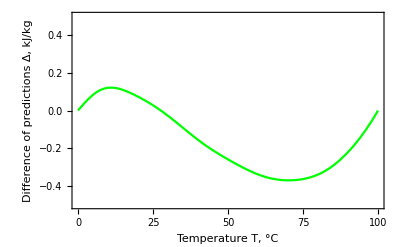

```mathematica
difeng=Plot[avcap(100-T)-Integrate[cap[t],{t,T,100}],{T,0.01,100},ImageSize->{1000},PlotRange->{{0,100},{-0.5,0.5}},Axes->{True,False},Frame->True,AxesLabel->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Temperature T, °C",28,FontFamily->"Times New Roman"],Style["Difference of predictions Δ, kJ/kg",28,FontFamily->"Times New Roman"]},PlotStyle->Green]
```

```mathematica
-2.26-avcap 0.1-0.3348
```

-3.01391